```mathematica
ClearAll[Ausgleichsgerade];
Ausgleichsgerade[xValues_,yValues_]:=(
If[Length[xValues]==Length[xValues],,Throw["Arrays sind nicht gleich lang"]
];
ClearAll[n,xxValues,xyValues,Δ,xSum,ySum,xxSum,xySum,a,b,s2,σa,σb,Δc,yTrue,σy];

n=Length[xValues];

xxValues=Table[xValues[[i]]^2,{i,1,n}];
xyValues=Table[xValues[[i]]*yValues[[i]],{i,1,n}];

xSum=Sum[xValues[[i]],{i,1,n}];
ySum=Sum[yValues[[i]],{i,1,n}];
xxSum=Sum[xxValues[[i]],{i,1,n}];
xySum=Sum[xyValues[[i]],{i,1,n}];

Δ=n*xxSum-xSum^2;
a=1/Δ*(xxSum*ySum-xSum*xySum);
b=1/Δ*(n*xySum-xSum*ySum);

s2=1/(n-2)*Sum[(yValues[[i]]-a-b*xValues[[i]])^2,{i,1,n}];
σa=√(s2/Δ*xxSum);
σb=√(n*s2/Δ);

x=xSum/n;
y=ySum/n;
Δc=√(x^2*σb^2+σa^2);

yTrue=Table[b*xValues[[i]]+a,{i,1,n}];
σy=Table[(yValues[[i]]-yTrue[[i]])^2,{i,1,n}];
yTrueSum=Sum[yTrue[[i]],{i,1,n}];
σySum=Sum[σy[[i]],{i,1,n}];

Print["\n",TableForm[{Join[xValues,{"",xSum}],Join[yValues,{"",ySum}],Join[yTrue,{"",yTrueSum}],Join[σy,{"",σySum}],Join[xxValues,{"",xxSum}],Join[xyValues,{"",xySum}]},TableDirections->Row,TableSpacing->{3, 1},TableHeadings->{{"x_i", "y_i","y","(y-y_i)^2","x_i^2","x_i*y_i" },Join[Table["",{i,1,n+1}],{"Sum:"}]}]];
Print["\n","a = ",a," ± ",σa,"\n","b = ",b," ± ",σb,"\n","x̄ = ",x,"; ȳ = ",y,"; Δc = ",Δc];
Print["\n","=> y = (b ± Δb)*(x - x̄) + (ȳ ± Δc)","\n","=> y = (",b," ± ",σb,")*(x - ",x,") + ",y," ± ",Δc];
Show[{
ListPlot[Table[{xValues[[i]],yValues[[i]]},{i,1,n}],PlotStyle->Red,PlotMarkers->"X"],
Plot[{
(b)*(xCoord-x)+y,
(b+σb)*(xCoord-x)+y+Δc,
(b-σb)*(xCoord-x)+y+Δc,
(b+σb)*(xCoord-x)+y-Δc,
(b-σb)*(xCoord-x)+y-Δc
},
{xCoord,0,9},
PlotStyle->{Automatic,RGBColor[169/256,195/256,97/256,0.7],RGBColor[169/256,195/256,97/256,0.7],RGBColor[230/256,171/256,68/256,0.7],RGBColor[230/256,171/256,68/256,0.7]}
]
},ImageSize->Full]
)
```

| x_i | y_i | y | (y-y_i)^2 | x_i^2 | x_i*y_i
 | 0.2 | 52.4 | 52.6816 | 0.0793235 | 0.04 | 10.48
 | 1.17 | 54.6 | 55.1071 | 0.257117 | 1.3689 | 63.882
 | 1.96 | 57.7 | 57.0824 | 0.381415 | 3.8416 | 113.092
 | 2.98 | 59.5 | 59.6329 | 0.0176509 | 8.8804 | 177.31
 | 4.05 | 62.7 | 62.3083 | 0.153411 | 16.4025 | 253.935
 | 5.12 | 65.6 | 64.9838 | 0.379715 | 26.2144 | 335.872
 | 5.93 | 67. | 67.0091 | 0.0000835943 | 35.1649 | 397.31
 | 7.01 | 69. | 69.7096 | 0.503552 | 49.1401 | 483.69
 | 8.24 | 72.8 | 72.7852 | 0.000220513 | 67.8976 | 599.872
 |  |  |  |  |  | 
Sum: | 36.66 | 561.3 | 561.3 | 1.77249 | 208.95 | 2435.44

a = 52.1816 ± 0.314007
b = 2.50044 ± 0.0651688
x̄ = 4.07333; ȳ = 62.3667; Δc = 0.411177

=> y = (b ± Δb)*(x - x̄) + (ȳ ± Δc)
=> y = (2.50044 ± 0.0651688)*(x - 4.07333) + 62.3667 ± 0.411177

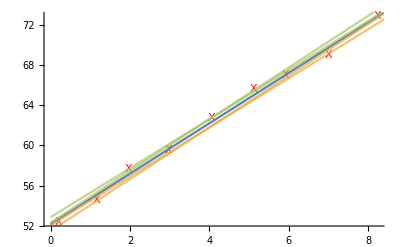

```mathematica
xValues={0.20,1.17,1.96,2.98,4.05,5.12,5.93,7.01,8.24};
yValues={52.4,54.6,57.7,59.5,62.7,65.6,67.0,69.0,72.8};

Ausgleichsgerade[xValues,yValues]
```